```mathematica
Check the error amplitude dependence of dr
```

```mathematica
Timing[
ClearAll[V,clight,m,q,R,l,Bz0,De,orb,Aθ,LENG,x,y,z,vx,vy,vz,gamma,RS,CAM,CAMSCALE,S,MaxPtN];

(*Parameter list in order to read simuilation data files*)

V[1]={"0","1","2","3"};
V[2]={"nr51_nz2001","nr101_nz2001","nr151_nz2001","nr201_nz2001"};

(*Needed physical parameters*)

clight=2.99792458*10^8;(*Speed of light*)
m=238*1.66053892*10^-27;(*Mass of particle*)
q=34*1.60217657*10^-19;(*Charge of particle*)
R=0.08;(*Solenoid radius*)
l=0.3;(*Solenoid length*)
Bz0=1.7647058823529411;(*Scaling factor for magnetic fields*)
De[1]={100,100,100,100};(*Thin down datas to reduce a calculation time*)

(* Read in data file: put your directory path here *)

Table[orb[i,j]=Import["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Warp_Change_dr/orbit"<>ToString[V[1][[i]]]<>"_Lz20_"<>ToString[V[2][[j]]]<>"_Vz3e7_Bz1.0_NStep100000.dat","Table"],{i,1,4},{j,1,4}];

Aθ[r_,z_]:=NIntegrate[(R^2*r)/(2π)((Sin[θ]*Sin[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ]))),{θ,0,2π}]/(Bz0);

(*Vector potential of thin coil solenoid*)

Table[LENG[i,j]=Length[orb[i,j]],{i,1,4},{j,1,4}];(*Count the lines of each data file*)

(*Make lists of particle orbits*)

Table[x[i,j]=orb[i,j][[All,2]],{i,1,4},{j,1,4}];
Table[y[i,j]=orb[i,j][[All,3]],{i,1,4},{j,1,4}];
Table[z[i,j]=orb[i,j][[All,4]],{i,1,4},{j,1,4}];
Table[vx[i,j]=orb[i,j][[All,5]],{i,1,4},{j,1,4}];
Table[vy[i,j]=orb[i,j][[All,6]],{i,1,4},{j,1,4}];
Table[vz[i,j]=orb[i,j][[All,7]],{i,1,4},{j,1,4}];

(*Lorentz factor gamma and radial amplitude for each simulation step*)

Table[gamma[i,j]=√(1/(1-((vx[i,j]^2+vy[i,j]^2+vz[i,j]^2)/clight^2))),{i,1,4},{j,1,4}];
Table[RS[i,j]=Table[√(x[i,j][[n]]*x[i,j][[n]]+y[i,j][[n]]*y[i,j][[n]]),{n,1,LENG[i,j]}],{i,1,4},{j,1,4}];

(*Not scaled and scaled canonical angular momentum vs z*)

Table[CAM[i,j]=Table[{z[i,j][[n]],10^6*(m*gamma[i,j][[n]]*(x[i,j][[n]]*vy[i,j][[n]]-y[i,j][[n]]*vx[i,j][[n]])+q*Aθ[RS[i,j][[n]],z[i,j][[n]]]*RS[i,j][[n]])/(m*clight)},{n,1,LENG[i,j],De[1][[j]]}],{i,1,4},{j,1,4}];

Table[CAMSCALE[i,j]=Table[{z[i,j][[n]],CAM[i,j][[1+(n-1)/De[1][[j]],2]]/(CAM[i,j][[1,2]])},{n,1,LENG[i,j],De[1][[j]]}],{i,1,4},{j,1,4}];

(*Making lists of dr vs maxmum error amplitude*)

S[1]={1.6/0.5,1.6/1,1.6/1.5,1.6/2};
Table[MaxPtN[i,j]={S[1][[j]],Max[CAMSCALE[i,j][[All,2]]]},{i,1,4},{j,1,4}];

]
```

{99.1808,Null}

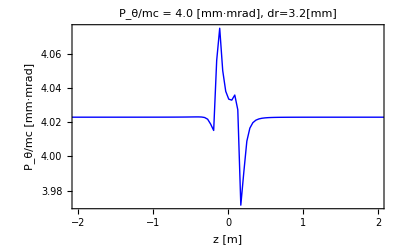

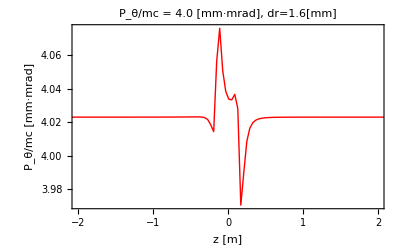

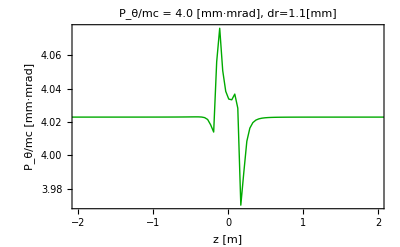

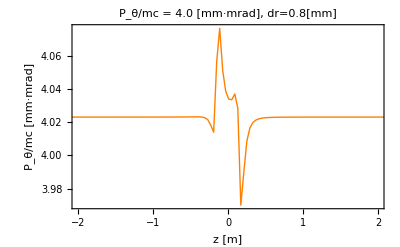

```mathematica
(*P_theta/mc vs z with several dr*)

PT[1]=ListPlot[CAM[4,1],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Blue},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=3.2[mm]",17]]
PT[2]=ListPlot[CAM[4,2],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Red},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=1.6[mm]",17]]
PT[3]=ListPlot[CAM[4,3],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Darker[Green]},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=1.1[mm]",17]]
PT[4]=ListPlot[CAM[4,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Orange},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=0.8[mm]",17]]
```

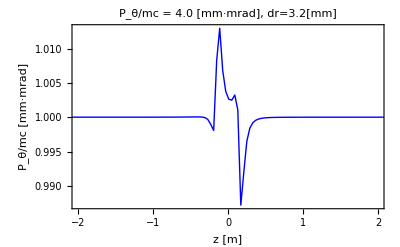

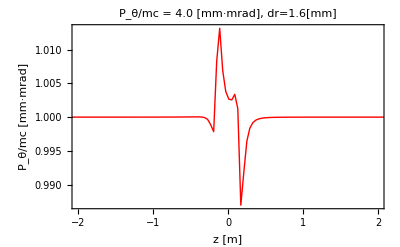

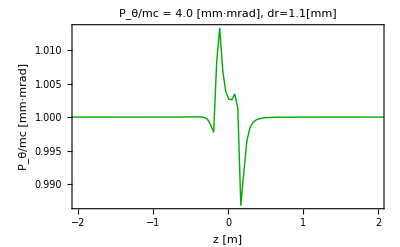

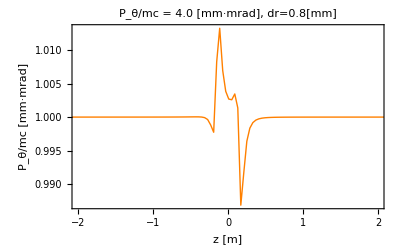

```mathematica
(*Scaled P_theta/mc vs z with several dr*)

PS[1]=ListPlot[CAMSCALE[4,1],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Blue},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=3.2[mm]",17]]
PS[2]=ListPlot[CAMSCALE[4,2],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Red},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=1.6[mm]",17]]
PS[3]=ListPlot[CAMSCALE[4,3],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Darker[Green]},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=1.1[mm]",17]]
PS[4]=ListPlot[CAMSCALE[4,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Orange},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad], dr=0.8[mm]",17]]
```

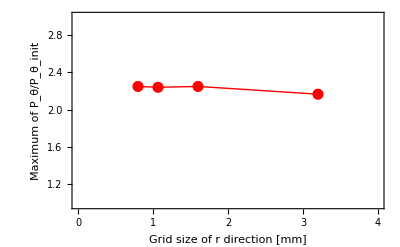

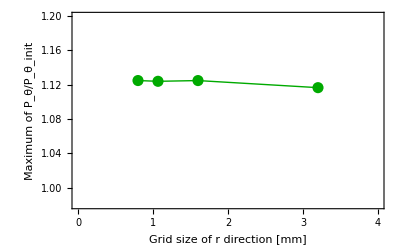

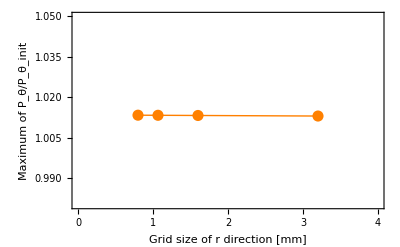

```mathematica
(*Maxmum error amplitude vs dr*)

SPt[1]=Show[
ListPlot[Table[MaxPtN[2,j],{j,1,4}],PlotStyle->{PointSize[0.02],Red},Axes->None,Frame->True,Joined->True,FrameLabel->{"Grid size of r direction [mm]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[17],PlotRange->{{0,4},{0.98,3}}],
ListPlot[Table[MaxPtN[2,j],{j,1,4}],PlotStyle->{PointSize[0.02],Red},Axes->None,Frame->True,FrameLabel->{"z [m]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[18]]
]

SPt[2]=Show[
ListPlot[Table[MaxPtN[3,j],{j,1,4}],PlotStyle->{PointSize[0.02],Darker[Green]},Axes->None,Frame->True,Joined->True,FrameLabel->{"Grid size of r direction [mm]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[17],PlotRange->{{0,4},{0.98,1.2}}],
ListPlot[Table[MaxPtN[3,j],{j,1,4}],PlotStyle->{PointSize[0.02],Darker[Green]},Axes->None,Frame->True,FrameLabel->{"z [m]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[18]]
]

SPt[3]=Show[
ListPlot[Table[MaxPtN[4,j],{j,1,4}],PlotStyle->{PointSize[0.02],Orange},Axes->None,Frame->True,Joined->True,FrameLabel->{"Grid size of r direction [mm]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[17],PlotRange->{{0,4},{0.98,1.05}}],
ListPlot[Table[MaxPtN[4,j],{j,1,4}],PlotStyle->{PointSize[0.02],Orange},Axes->None,Frame->True,FrameLabel->{"z [m]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[18]]
]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr_Norm_emit_4e-8.eps",SPt[1],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr_Norm_emit_4e-7.eps",SPt[2],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr_Norm_emit_4e-6.eps",SPt[3],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr51_Pthe_time_evol_4e-6.eps",PT[1],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr101_Pthe_time_evol_4e-6.eps",PT[2],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr151_Pthe_time_evol_4e-6.eps",PT[3],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr201_Pthe_time_evol_4e-6.eps",PT[4],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr51_PtheN_time_evol_4e-6.eps",PS[1],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr101_PtheN_time_evol_4e-6.eps",PS[2],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr151_PtheN_time_evol_4e-6.eps",PS[3],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_dr/Nr201_PtheN_time_evol_4e-6.eps",PS[4],"EPS"];
```